# Numerical solution for two - level system .

```mathematica
Clear["Global`*"]
```

### Hamiltonian, density matrix and decay matrix

```mathematica
rho = {{r11[t], r12[t]},{r21[t], r22[t]}};
r1 = {{r11, r12},{r21, r22}};
rho1 = Flatten[rho];
H={{  0 ,-Ω/2},{-Ω/2,Δ}};
Λ= {{0,0},{0,Γ}};
repop = {{Γ r22[t] ,0},{0,0}};
comm =(H.rho - rho.H);
anticomm = Λ.rho +rho.Λ
```

{{0,Γ r12[t]},{Γ r21[t],2 Γ r22[t]}}

```mathematica
Ω =1;
Γ =0.15;
Δ=0;
```

```mathematica
eqTable = Table[r1[[i,j]]'[t]==-I (comm[[i,j]])-1/2 anticomm[[i,j]]+repop[[i,j]],{i,1,2},{j,1,2}]
eqs = Join[Flatten[eqTable],{r11[0]==1,r12[0]==0, r21[0]==0,r22[0]==0}];
solution=NDSolve[eqs,rho1,{t,0,50}];
```

{{r11'[t]==-ⅈ (r12[t]/2-r21[t]/2)+0.15 r22[t],r12'[t]==-0.075 r12[t]-ⅈ (r11[t]/2-r22[t]/2)},{r21'[t]==-0.075 r21[t]-ⅈ (-r11[t]/2+r22[t]/2),r22'[t]==-ⅈ (-r12[t]/2+r21[t]/2)-0.15 r22[t]}}

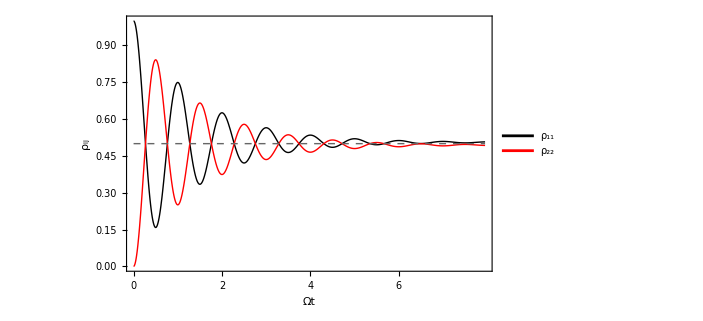

```mathematica
(*Assume'solution' is as returned by NDSolve,and rho1[[1]]=r11,rho1[[2]]=r22*)(*Define how to extract the numerical solutions*)r11Plot[t_]:=Evaluate[r11[t]/. solution]
r22Plot[t_]:=Evaluate[r22[t]/. solution]

(*Now plot r11 and r22 versus time,with the x-axis labeled in units of 2 Pi*)
p=Plot[{r11Plot[t],r22Plot[t],0.5},{t,0,50},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->All,
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],
FrameTicks->{{Automatic,None},{Table[{2 Pi n,ToString[n]},{n,0,Floor[50/(2 Pi)]}],None}},
PlotStyle->{Directive[Black,Thick],(*y1:solid thick blue*)
Directive[Red,Thick](*y2:solid thick orange*), 
Directive[GrayLevel[0.4],Dashed,Thick]},
FrameLabel->{Style["Ωt",Bold,14],Style["ρ_ij",Bold,14]},PlotLegends->Placed[LineLegend[{"ρ_11","ρ_22"},LabelStyle->{FontSize->12}],{0.9,0.9} (*{x,y} in scaled coordinates (0=start,1=end)*)],
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
ImageSize->Large]
```

```mathematica
Export["/home/nayan/Desktop/diagrams/for thesis/osscdecay.pdf",p, ImageResolution->300];
```